```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

checkpoint 3

checkpoint 4

checkpoint 1

checkpoint 2

Select::normal: Nonatomic expression expected at position 1 in Select[googleMobility,#1[country_region_code]==US&&#1[sub_region_1]==California&&#1[sub_region_2]==&].

DateDifference::date: Expression DateObject[googleMobility[date]] cannot be interpreted as a date specification.

DateDifference::date: Expression DateObject[date[country_region_code]==US&&date[sub_region_1]==California&&date[sub_region_2]==] cannot be interpreted as a date specification.

QuantityMagnitude::argt: QuantityMagnitude called with 0 arguments; 1 or 2 arguments are expected.

Last::nolast: QuantityMagnitude[] has zero length and no last element.

DatePlus::inc: -1+Last[QuantityMagnitude[]] is not a recognized calendar increment specification for DatePlus.

DateString::arg: Argument DatePlus[DateObject[{2020,1,1},Day,Gregorian,-7.],-1+Last[QuantityMagnitude[]]] cannot be interpreted as a date or time input or as a date string format.

Fitting model for CA

>> <|chiSquared→3.97937×10^-6,rmsRelativeError→0.414278,rmsRelativeErrorDeaths→0.270494,rmsRelativeErrorPcr→0.499357,meanRelativeErrorDeaths→0.0742958,meanRelativeErrorPcr→-0.168855,rSquaredDeaths→0.188365,rSquaredPcr→0.0342291,deathResidual7Day→-0.257623,pcrResidual7Day→42.0447|>

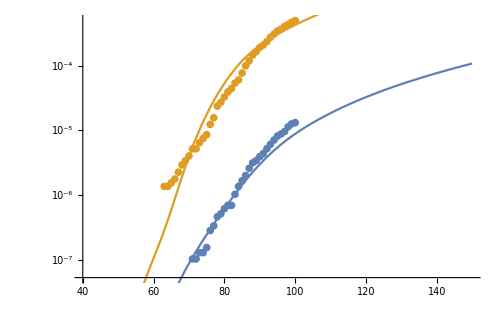
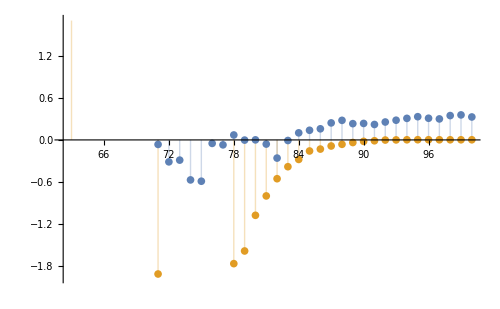
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.10701 | 0.00724075 | 429.101 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[429.101,64.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 51.9797 | 0.0472505 | 1100.09 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[1100.09,64.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.45251 | 0.0907286 | 16.0094 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[16.0094,64.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.68156 | 0.253488 | 6.63371 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[6.63371,64.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 1.09148×10^-9 | 2.72871×10^-10
Error | 64 | 5.50995×10^-11 | 8.6093×10^-13
Uncorrected Total | 68 | 1.14658×10^-9 | 
Corrected Total | 67 | 1.12659×10^-9 |

>> Current Indefinite scenario Generating simulations for CA in the

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

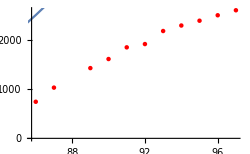
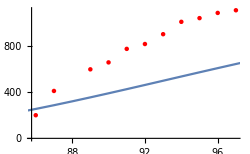
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

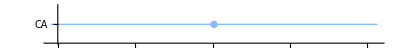
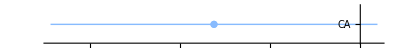
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfPCRHospitalized | fractionHospitalizedInICU | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario5 | 629 | True | Current Indefinite | <|"totalProjectedDeaths" -> 19641.868631398596, "totalProjectedPCRConfirmed" -> 541501.292246634, "totalProjectedInfected" -> 3.1473994932415923*^6, "totalInfectedFraction" -> 0.08073806136431216, "fatalityRate" -> 0.006199856943505006, "fatalityRateSymptomatic" -> 0.011745308854340329, "fatalityRatePCR" -> 0.03399774804426714, "fractionOfSymptomaticHospitalized" -> 0.16466880144159135, "fractionOfPCRHospitalized" -> 0.6140015028648727, "fractionHospitalizedInICU" -> 0.22729433619367473, "fractionOfInfectionsPCRConfirmed" -> 0.11252277220361487, "dateContained" -> "Fri 2 Jul 2021 00:00:00", "dateICUOverCapacity" -> "Sun 5 Jul 2020 09:45:29", "dateHospitalsOverCapacity" -> "Sat 1 Aug 2020 07:26:02"|> | 59192.4 | 2.13636×10^6 | 6.28798×10^6 | 0.161301 | 0.00825411 | 0.0151586 | 0.0247394 | 0.180057 | 0.638437 | 0.245759 | 0.233517 | Fri 2 Jul 2021 00:00:00 | Sun 5 Jul 2020 09:45:29 | Sat 1 Aug 2020 07:26:02 | 3.10701 | 51.9797 | 1.45251
CA | 81/140 | scenario1 | 90 | True | Current | <|"totalProjectedDeaths" -> 26212.572658141806, "totalProjectedPCRConfirmed" -> 1.2867903880144875*^6, "totalProjectedInfected" -> 8.463471079232493*^6, "totalInfectedFraction" -> 0.2171075673162736, "fatalityRate" -> 0.003879556507384905, "fatalityRateSymptomatic" -> 0.008236161252345671, "fatalityRatePCR" -> 0.025119354783244164, "fractionOfSymptomaticHospitalized" -> 0.12989227175991702, "fractionOfPCRHospitalized" -> 0.5531658395663721, "fractionHospitalizedInICU" -> 0.25261495981897814, "fractionOfInfectionsPCRConfirmed" -> 0.0853822155267655, "dateContained" -> "Tue 8 Dec 2020 00:00:00", "dateICUOverCapacity" -> "Sun 5 Jul 2020 09:45:29", "dateHospitalsOverCapacity" -> "Tue 21 Jul 2020 12:43:49"|> | 271792. | 1.09796×10^7 | 2.84354×10^7 | 0.729433 | 0.00926296 | 0.0165598 | 0.0237367 | 0.175666 | 0.644965 | 0.245761 | 0.243817 | Tue 8 Dec 2020 00:00:00 | Sun 5 Jul 2020 09:45:29 | Tue 21 Jul 2020 12:43:49 | 3.10701 | 51.9797 | 1.45251
CA | 0.4 | scenario2 | 90 | False | Italy | <|"totalProjectedDeaths" -> 2718.27776620656, "totalProjectedPCRConfirmed" -> 70675.62761165119, "totalProjectedInfected" -> 421413.032408088, "totalInfectedFraction" -> 0.010810216924589628, "fatalityRate" -> 0.008771211978753636, "fatalityRateSymptomatic" -> 0.0164042884924183, "fatalityRatePCR" -> 0.053199004404392874, "fractionOfSymptomaticHospitalized" -> 0.16924203181935535, "fractionOfPCRHospitalized" -> 0.616474434451637, "fractionHospitalizedInICU" -> 0.24729955104431253, "fractionOfInfectionsPCRConfirmed" -> 0.10199450374087349, "dateContained" -> "Wed 1 Jul 2020 00:00:00", "dateICUOverCapacity" -> "Thu 27 Aug 2020 00:37:33", "dateHospitalsOverCapacity" -> "Thu 27 Aug 2020 01:50:01"|> | 297019. | 1.33421×10^7 | 2.88889×10^7 | 0.741066 | 0.00960001 | 0.0178641 | 0.02099 | 0.174639 | 0.632901 | 0.245761 | 0.294385 | Wed 1 Jul 2020 00:00:00 | Thu 27 Aug 2020 00:37:33 | Thu 27 Aug 2020 01:50:01 | 3.10701 | 51.9797 | 1.45251
CA | 0.11 | scenario3 | 60 | False | Wuhan | <|"totalProjectedDeaths" -> 2894.659052706939, "totalProjectedPCRConfirmed" -> 66649.8667180708, "totalProjectedInfected" -> 419117.29076888144, "totalInfectedFraction" -> 0.01075132585285219, "fatalityRate" -> 0.0063953032683016515, "fatalityRateSymptomatic" -> 0.013004686434320074, "fatalityRatePCR" -> 0.04073280765067465, "fractionOfSymptomaticHospitalized" -> 0.1636219352858298, "fractionOfPCRHospitalized" -> 0.6028312346166749, "fractionHospitalizedInICU" -> 0.2529915082772255, "fractionOfInfectionsPCRConfirmed" -> 0.09602984648178702, "dateContained" -> "Tue 12 May 2020 00:00:00", "dateICUOverCapacity" -> "Wed 26 Aug 2020 23:11:08", "dateHospitalsOverCapacity" -> "Wed 26 Aug 2020 23:57:40"|> | 250341. | 1.42184×10^7 | 2.93265×10^7 | 0.752292 | 0.00869217 | 0.0146917 | 0.0182857 | 0.175489 | 0.644405 | 0.245761 | 0.292071 | Tue 12 May 2020 00:00:00 | Wed 26 Aug 2020 23:11:08 | Wed 26 Aug 2020 23:57:40 | 3.10701 | 51.9797 | 1.45251
CA | 1 | scenario4 | 90 | False | Normal | <|"totalProjectedDeaths" -> 255982.91951418345, "totalProjectedPCRConfirmed" -> 5.231290368825317*^6, "totalProjectedInfected" -> 2.944024269986737*^7, "totalInfectedFraction" -> 0.7552101748717166, "fatalityRate" -> 0.008372858789927178, "fatalityRateSymptomatic" -> 0.015073843745969314, "fatalityRatePCR" -> 0.04730728331724715, "fractionOfSymptomaticHospitalized" -> 0.17708978154142904, "fractionOfPCRHospitalized" -> 0.6403058780226387, "fractionHospitalizedInICU" -> 0.2412717661374429, "fractionOfInfectionsPCRConfirmed" -> 0.11205428205035792, "dateContained" -> "Sun 13 Sep 2020 00:00:00", "dateICUOverCapacity" -> "Wed 6 May 2020 03:45:44", "dateHospitalsOverCapacity" -> "Wed 6 May 2020 07:10:43"|> | 262268. | 5.24876×10^6 | 2.94938×10^7 | 0.756583 | 0.00855268 | 0.0154282 | 0.0482057 | 0.178104 | 0.641358 | 0.245761 | 0.113755 | Sun 13 Sep 2020 00:00:00 | Wed 6 May 2020 03:45:44 | Wed 6 May 2020 07:10:43 | 3.10701 | 51.9797 | 1.45251

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```